# Research

```mathematica
token = "Bearer c3faccf686261ebf44cd1fe0954185ace3d018ae";
```

All tasks:

```mathematica
ItemList[itemType_String:"tasks"]:= Association /@ Import[ 
URLRead[ 
HTTPRequest[
<| 
"Scheme" -> "https", 
"Domain" -> "api.todoist.com", 
"Path" -> "rest/v1/"<>itemType, 
"Headers" -> {
"Authorization" -> token
}
|>
]
]
]

ListToAssociation[list_List]:=Association[#["id"]->#&/@list]
```

```mathematica
TasksAssociation[]:=Select[ListToAssociation[ItemList["tasks"]], !#["completed"]&]
```

## Task graph

### Working with ids only

```mathematica
tasks = TasksAssociation[];
```

```mathematica
First@tasks
```

<|id→3080365876,project_id→2227344287,section_id→0,parent→3631656472,order→2,content→Google Tutorials, work in Google,completed→False,label_ids→{},priority→3,comment_count→0,created→2019-03-03T15:52:37Z,url→https://todoist.com/showTask?id=3080365876|>

```mathematica
GetGraph[items_, labelKey_:"content"]:=Module[
{
allIds=Keys[items],
idsRelations=Select[#["id"]->#["parent"]&/@Values[items],!MissingQ[Last[#]]&],
vertexStyles=Automatic,
vertexLabels,
QPriority=KeyExistsQ[First[items], "priority"]
},
If[
QPriority,
vertexStyles = Normal[Switch[#["priority"], 1, Gray, 2, Blue, 3, Yellow, 4, Red]&/@items]
];
vertexLabels = Normal[#[labelKey]&/@items];
Graph[
allIds, 
idsRelations,
GraphLayout->"RadialEmbedding",
PlotTheme->"Scientific",
DirectedEdges->True,
VertexStyle->vertexStyles,
VertexLabels->vertexLabels
]
]
```

```mathematica
tasksGraph=GetGraph[tasks]
```

-Graphics-

```mathematica
Show[#,ImageSize->Large]&/@WeaklyConnectedGraphComponents[tasksGraph][[1;;5]]//Column
```

-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-

### Select tasks at bottom of tree: zero indegree

#### Zero indegree tasks

```mathematica
ZeroInDegreeTasks[taskList_, taskGraph_]:=Pick[taskList,#==0&/@VertexInDegree[taskGraph]]
```

```mathematica
ZeroInDegreeTasks[tasks, tasksGraph][[1;;4]]
```

<|3080365876→<|id→3080365876,project_id→2227344287,section_id→0,parent→3631656472,order→2,content→Google Tutorials, work in Google,completed→False,label_ids→{},priority→3,comment_count→0,created→2019-03-03T15:52:37Z,url→https://todoist.com/showTask?id=3080365876|>,3080366916→<|id→3080366916,project_id→2206555710,section_id→0,order→4,content→Naming Conventions,completed→False,label_ids→{},priority→1,comment_count→0,created→2019-03-03T15:53:40Z,url→https://todoist.com/showTask?id=3080366916|>,3080367231→<|id→3080367231,project_id→2206555710,section_id→0,order→6,content→Licenses,completed→False,label_ids→{},priority→1,comment_count→0,created→2019-03-03T15:53:56Z,url→https://todoist.com/showTask?id=3080367231|>,3080367862→<|id→3080367862,project_id→2206555710,section_id→0,order→2,content→Друкувути не дивлячись на клавіатуру,completed→False,label_ids→{},priority→2,comment_count→0,created→2019-03-03T15:54:30Z,url→https://todoist.com/showTask?id=3080367862|>|>

## Prioritisation of tasks

### priorityFucntion

Time

```mathematica
timePriorFunc[time_,priority_:1, k_:0.05, maxPriotity_:22]:=Max[maxPriotity(1+priority^3)/(1+4^3)If[time>0,Exp[-time*k], 0.85],priority]//N//Quiet
```

```mathematica
PrioritySelector[days_]:=Which[
days==0, 0, 
days>0&& days<=2, 30,
days>2&& days≤7, 15,
days>7&&days≤31,10,
days<0, 6,
days>0, 2];
```

```mathematica
Manipulate[
Plot[
{
timePriorFunc[days,1,k,maxValue],
timePriorFunc[days,2,k,maxValue],
timePriorFunc[days,3,k,maxValue],
timePriorFunc[days,4,k,maxValue],
PrioritySelector[days]
},
{days, -3,30},
AxesLabel->{"Days","Priority"},
PerformanceGoal->"Quality",
MaxRecursion->5,
PlotLegends->{1,2,3,4, "Old"},
PlotRange->{All, {0,30}}
],
{{maxValue, 30}, 1, 30},
{{k,0.06},0,0.5}
]
```

```mathematica
TaskPriority[task_]:=Module[
{
currentTime=UnixTime[],
hasDueKey=KeyExistsQ[task, "due"],
taskPriority=task["priority"],
dTime=100
},
If[hasDueKey, dTime = (UnixTime[task["due"][[3, 2]]]-currentTime)/24/3600];
timePriorFunc[dTime, taskPriority, 0.06, 30]
]
```

```mathematica
TaskWeights[tasks_]:=#/Total[#]&@(TaskPriority[#]&/@tasks);
```

### Random task selection

```mathematica
SelectRandomlyTaskId[tasksWeightsAssoc_]:=RandomChoice[Values[tasksWeightsAssoc]->Keys[tasksWeightsAssoc]];
```

### Sorted tasks

```mathematica
SortedTasks[proj_Association,tasks_Association]:= 
#["title"]&/@SortBy[
MapThread[
<|{
"title"->proj[#1["project_id"],"name"]<>": "<>#1["content"], 
"priority"->#2
}|>&,
{
tasks,
TaskWeights[tasks]
}
],
-#["priority"]&
];
```

### Sorted tasks without projects names

```mathematica
SortedTasksSimplified[tasks_Association]:= 
#["title"]&/@SortBy[
MapThread[
<|{
"title"->#1["content"], 
"priority"->#2
}|>&,
{
tasks,
TaskWeights[tasks]
}
],
-#["priority"]&
];
```

## WordCloud

```mathematica
PlotTaskCloud[tasks_, number_:20]:=Module[
{
words=Values[#["content"]&/@tasks], 
weights=Abs[Values@TaskWeights[tasks]]
},
WordCloud[weights[[-number;;-1]]->words[[-number;;-1]],ImageSize->Large]
];
```

```mathematica
tasks = TasksAssociation[];
```

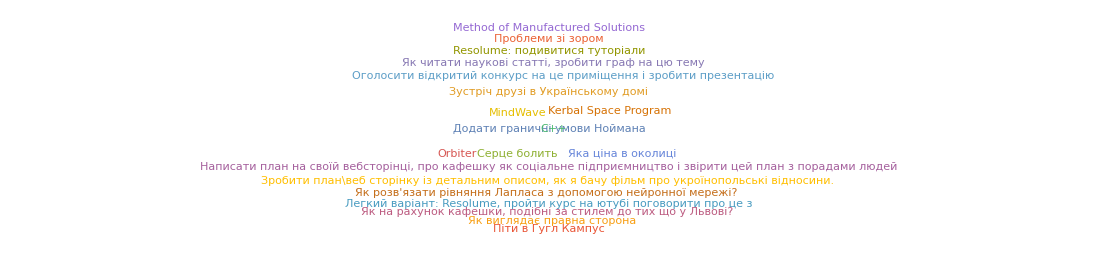

```mathematica
PlotTaskCloud[tasks]
```

All projects

```mathematica
ProjectsAssociation[]:=Association[#["id"]->#&/@ItemList["projects"]]
```

```mathematica
ProjectsAssociation[]
```

<|2206555164→<|id→2206555164,color→48,name→Inbox,comment_count→0,shared→False,inbox_project→True|>,2206555718→<|id→2206555718,order→11,color→34,name→Робота, підприємництво та ідеї,comment_count→0,shared→False|>,2219925609→<|id→2219925609,order→12,color→41,name→Science,comment_count→0,shared→False|>,2227344014→<|id→2227344014,order→14,color→30,name→Навчання,comment_count→0,shared→False|>,2219351378→<|id→2219351378,order→15,color→32,name→Personal,comment_count→0,shared→False|>,2227344634→<|id→2227344634,parent→2206555710,order→1,color→33,name→Криптографія\Безпека\Криптовалюта,comment_count→0,shared→False|>,2227344656→<|id→2227344656,parent→2206555710,order→2,color→38,name→Unity3D,comment_count→0,shared→False|>,2227344287→<|id→2227344287,parent→2206555718,order→1,color→34,name→Перша робота в Польщі,comment_count→0,shared→False|>,2225986788→<|id→2225986788,parent→2206555718,order→3,color→34,name→Візуальні ефекти,comment_count→3,shared→False|>,2225938311→<|id→2225938311,parent→2206555718,order→4,color→30,name→Artemis,comment_count→0,shared→False|>,2227494251→<|id→2227494251,parent→2206555718,order→5,color→44,name→Альтернативна енергетика,comment_count→0,shared→False|>,2229542999→<|id→2229542999,parent→2206555718,order→7,color→34,name→Домашнє підприємництво,comment_count→0,shared→False|>,2228063623→<|id→2228063623,parent→2206555765,order→1,color→42,name→Plan B,comment_count→0,shared→False|>,2230451604→<|id→2230451604,parent→2208326982,order→1,color→38,name→Документальний фільм,comment_count→0,shared→False|>,2208326852→<|id→2208326852,parent→2219351378,order→1,color→40,name→Music,comment_count→0,shared→False|>,2206555765→<|id→2206555765,parent→2219351378,order→2,color→39,name→Home,comment_count→0,shared→False|>,2208326982→<|id→2208326982,parent→2219351378,order→3,color→46,name→Social,comment_count→0,shared→False|>,2206555729→<|id→2206555729,parent→2219351378,order→4,color→35,name→Здоров'я,comment_count→0,shared→False|>,2206555741→<|id→2206555741,parent→2219351378,order→5,color→36,name→Shopping,comment_count→0,shared→False|>,2206555753→<|id→2206555753,parent→2219351378,order→6,color→38,name→Blog,comment_count→0,shared→False|>,2206555680→<|id→2206555680,parent→2219925609,order→1,color→31,name→RiverSim,comment_count→0,shared→False|>,2227344319→<|id→2227344319,parent→2219925609,order→3,color→41,name→Комп'ютерна фізика і комп'ютерні науки,comment_count→0,shared→False|>,2227344340→<|id→2227344340,parent→2219925609,order→4,color→41,name→AI у фізиці,comment_count→0,shared→False|>,2227344453→<|id→2227344453,parent→2219925609,order→6,color→39,name→Автоматичні доведення,comment_count→0,shared→False|>,2227579175→<|id→2227579175,parent→2225986788,order→1,color→40,name→DownTown,comment_count→0,shared→False|>,2206555692→<|id→2206555692,parent→2227344014,order→1,color→32,name→University,comment_count→0,shared→False|>,2225986809→<|id→2225986809,parent→2227344014,order→2,color→45,name→Самонавчання,comment_count→0,shared→False|>,2206555710→<|id→2206555710,parent→2227344014,order→3,color→33,name→Programming,comment_count→0,shared→False|>,2218823373→<|id→2218823373,parent→2227344014,order→4,color→45,name→Languages,comment_count→0,shared→False|>,2230587591→<|id→2230587591,parent→2227494251,order→1,color→41,name→MPPT Controller,comment_count→0,shared→False|>|>

## Projects graph

```mathematica
GetGraph[ProjectsAssociation[], "name"]
```

-Graphics-

All sections

```mathematica
SectionsAssociation[]:=ListToAssociation[ItemList["sections"]]
```

```mathematica
SectionsAssociation[]
```

<|4428228→<|id→4428228,project_id→2225986809,order→1,name→Курсера|>|>

# Final Program

```mathematica
CloudDeploy[
Manipulate[
Module[
{
proj=ProjectsAssociation[],
tasks=TasksAssociation[],
tasksGraph,
nonDependentTask ,
tasksWeightAssoc,
targetTaskID,
targetTask,
sortedTasks,
url
},

tasksGraph=GetGraph[tasks];
nonDependentTask=ZeroInDegreeTasks[tasks, tasksGraph];
tasksWeightAssoc=TaskWeights[nonDependentTask];

targetTaskID=SelectRandomlyTaskId[tasksWeightAssoc];
targetTask=tasks[targetTaskID];
sortedTasks=SortedTasks[proj,  nonDependentTask];
url=targetTask["url"];

Column[{
Button[
"Open random task", 
targetTaskID=SelectRandomlyTaskId[tasksWeightAssoc];
Print[targetTaskID];
targetTask=tasks[targetTaskID];
Print[targetTask];
sortedTasks=SortedTasks[proj,  nonDependentTask];
Print[sortedTasks];
url=targetTask["url"];
Print[url];
SystemOpen[url],
ImageSize->{400,100}
],
PlotTaskCloud[tasks],
Show[GetGraph[proj, "name"],ImageSize->Full],
Column[Values[sortedTasks]]
}]
],
"Todoist task random selector"
],
"WhatsNext",
CloudObjectNameFormat->"UserURLBase"
]
```

CloudObject[https://www.wolframcloud.com/obj/ofcrashbash/WhatsNext]